# Ethereum Testnet

Both the Bitcoin and Ethereum Testnets allow individuals to play around with their platforms without the risk of losing real financial assets. Though Bitcoin is designed to only permit one type of transaction, we can attach a message to this transaction for inclusion on the blockchain. Similarly, Ethereum also has the potential to include brief messages in their transactions.

```mathematica
(*Set default blockchain to Bitcoin testnet*)
BlockchainBase["Ethereum","Testnet"];

(*Create pair of keys for Bitcoin network*)
ethKeys=GenerateAsymmetricKeyPair["Ethereum","Testnet"];

(*Create a Bitcoin testnet address*)
ethAddress=BlockchainKeyEncode[ethKeys["PublicKey"],"Address"]

(*Get some fake Eth from the URL https://coinfaucet.eu/en/btc-testnet/ and save your transaction ID*)
sourceTXID="fdeb0754e9a9e25951979d818bd63bf4487985edf6317de2d8fad71b4dbdfb1a"; (*enter trx ID between quotes*)
sourceTX=BlockchainTransactionData[sourceTXID]
sourceTX["Outputs"]⟦2⟧
```

```mathematica
(*Make a transaction*)
change=UnitConvert[Lookup[sourceTX["Outputs"]⟦2⟧,"Amount"]-Quantity[10000., "Satoshis"]-Quantity[0.01, "Bitcoins"],"Bitcoins"]
tx=BlockchainTransaction[<|"Inputs"->{<|"TransactionID"->sourceTXID,"Index"->1|>},"Outputs"->{<|"Amount"->Quantity[0.01, "Bitcoins"],"Address"->"2MzEExewcCKYN8q7cKrSiZqHLk8NSbpjh1x"|>,<|"Amount"->change,"Address"->address|>},"BlockchainBase"->{"Bitcoin","Testnet"}|>]

(*Sign the trx*)
signedTX=BlockchainTransactionSign[tx,btcKeys]

(*Submit the trx*)
BlockchainTransactionSubmit[signedTX]
```

# Bitcoin Testnet

While it is not currently possible to embed messages into Bitcoin’s blockchain with a transaction, it is possible to have metadata attached to particular transaction using an online wallet such as offered by blockchain.info. When making a transaction from their website, one can include a “label” which could be viewed as subject line in an email.

Both the Bitcoin and Ethereum Testnets allow individuals to play around with their platforms without the risk of losing real financial assets. Though Bitcoin is designed to only permit one type of transaction, we can attach a message to this transaction for inclusion on the blockchain. Similarly, Ethereum also has the potential to include brief messages in their transactions.

```mathematica
(*Set default blockchain to Bitcoin testnet*)
BlockchainBase["Bitcoin","Testnet"];

(*Create pair of keys for Bitcoin network*)
btcKeys=GenerateAsymmetricKeyPair["Bitcoin"];

(*Create a Bitcoin testnet address*)
btcAddress=BlockchainKeyEncode[btcKeys["PublicKey"],"Address"]

(*Get some fake BTC from the URL https://coinfaucet.eu/en/btc-testnet/ and save your transaction ID*)
sourceTXID="fdeb0754e9a9e25951979d818bd63bf4487985edf6317de2d8fad71b4dbdfb1a"; (*enter trx ID between quotes*)
sourceTX=BlockchainTransactionData[sourceTXID]
sourceTX["Outputs"]⟦2⟧
```

```mathematica
(*Make a transaction*)
change=UnitConvert[Lookup[sourceTX["Outputs"]⟦2⟧,"Amount"]-Quantity[10000., "Satoshis"]-Quantity[0.01, "Bitcoins"],"Bitcoins"]
tx=BlockchainTransaction[<|"Inputs"->{<|"TransactionID"->sourceTXID,"Index"->1|>},"Outputs"->{<|"Amount"->Quantity[0.01, "Bitcoins"],"Address"->"2MzEExewcCKYN8q7cKrSiZqHLk8NSbpjh1x"|>,<|"Amount"->change,"Address"->address|>},"BlockchainBase"->{"Bitcoin","Testnet"}|>]

(*Sign the trx*)
signedTX=BlockchainTransactionSign[tx,btcKeys]

(*Submit the trx*)
BlockchainTransactionSubmit[signedTX]
```

```mathematica
Databin["EM6FHeXi", All]
```

Databin[…]

```mathematica
recentHashes=Normal[Dataset[Databin["EM6FHeXi", -60]]][[All,1,-1]]
```

{2272c12e3cf805157f5a98a38e5f6f6b046a649595bd60c4c4e41d0337b01b1d,5d48b80529ce207bf40b823937c6b8acee62ae47fd14e60ecf8fa266950cee28,38cec9598667be39fee3749f3c52458ec2948e7e4c31b20e0505801caec08aab,61de2e801e8bd64b180a7da6e268fcc94803050bc2a7d41a76a76bc9aecccfb2,53b5f93fa6ae6cbe0283a3471c155287b4ba416b026fef222c4fa5771ec70040,3b903977cdf3e895790990981301f6b30921dad04f52b25aa153d408e564e59f,3e160a901dbce66ad36213903c71a678f71f1f80cc684dbf426108542109261d,7df325e9298ceb75a8de3c81a66cd01937c8b8b482ae0ba1454501ffccf3f770,b49ca4eb74ece15dd9ec4d780bdeb365cbac401878281c5e02949dcf448d85d3,873e132d43838fbabcfde4d7eb596ff273cd64bb88e850bcd8e77f3228879097,218c4bda9b063b0c3972f9db01545e42d0f20a74854b9b0f1bf26e988d6f0c2d,9b74e31e0d7582c8469b1712cf8e2b2c6f0bf56e6e7afc5107c8bf441e3a7e2c,89db03683761323ed8eb84c98599e7d9c3fd5b9e8bec272b1b9ac78c0e11d2b7,e83a09db6fd25108abba0e5b9167a498a0266c24aab035881127546228a917c1,99da61cebc9cb9869868279f2d835aca118ef3be7dba7dba8be4b29ba201bb9e,931f8e95865998626b0e19886e1a852b185a12514692d2c370c9a82d30b8bbb6,01c04e195fc14e748e52966c2de6eb78b7bab53c2b431ecd9e9602089dfc6f2c,871980e17889f2388f1d9ecb112d68f9308e596ba915b4493dbf54a7f113c136,1f9314313a96338ebd3ef77df1f6f8bb186140c83517b96624d112d992ecfd8d,0a6e8af1d43a9a711be32c6259c175ff3ad553a6db3b0be86bac3c164867ea4d,545959e6f50d38077a074312dd3a41147e3a07b76cc5259e971742199d823476,2028b4310ff8169efccf4559871cb8a04bc2751852ea8ff8056b44b39ee04c56,3d751c1e32d67924ad286733062df40ecedc2943459de7b7683e5d10031d1bcc,5d631058718a2ce3e9efe84963bed2abbd573f91af15603d7d626b31f44f6000,1b042d6f1a7b20c67fac3a1b1e826b9aff56a426371c3452e5888bf282228202,76f89402ebff7ae418611a82a87766a4cd78e800e243130bccbbe28e89a3415e,bd4facf938d67181cdecdb13ae2b5b7c96660bc8ed568a57ca10b3bfa55b553f,edc69ba6a2b4009e9f247c41f986a19137ed06aafae766d194574713eedf58fa,49fe9dc199533e8644bbe7fde912463b0c4b2f4ecf5b8b5ff266d11785c354c3,035d6266f6e429aa21c1f77720a96facef75897a28e957bc14774ecfff6b3608,5e0c43cac3c9f0a1764ef8ce1835ae2d6b68e54ee57fe12831f87392fcf2bcfe,dabe1191f360e3c092757abaabca961bc1268d337d67ec9ba5fa1ce74f39c506,a081ed14e7095689b306fc198b501ea89553d1c6d1494b30043828fbdc657ac4,dfe006ec306beac11ea2b3c5e1a18e729d9b47782067d2b3cfda42ba9463f22a,f9e2762f0c947a9d28a856afc31e18687b52a14bbce8694f3cff4a66bd50fc0e,d629902235951dd608ae1dff4ab271d1204a3b545484907ee5c7e7765259af09,754531a06a90ec41db89b59399187e1b25b725ba16acd1bdf08a0aab75b5d475,6938d829009e66cb0c4d063d71a397ba769a0953fdd817e1060c63edd72267fd,ec3a8dfeb435754ae35ba7a006c79168056c58094302c1887773bcc3d95c4965,6063b086d7975b826909ec82d5b8be2930c4e55199c1631908e1d27062b5ac3c,18ec92ce6c61fdc54047950b901ef37a2af78e4fb2692e175279c969413d4abe,911285c99a8846dfab6def0ed0f8dd58c1e361638a8da22ab0ed07afc3cc55db,4fddae44a3b0dd25d3e754e2736303a3c3c253f1d4d52e255a46649973e7a6bd,70f398fdc4dd3101ff06a1fbc4252cbe0887a3299f847051feeadb35b1156afa,215b1a7d585b74eaa06d5c3d5b72430aad25e8a4e43b8cb8ff98eb1e3f250072,502aa158433706227267c24624984f4a28f05e2ab1896e8ad0310012e98bee8a,a7ae937163c2923c57924f29a8578a4040eec1564f26aa361305f02cbb926a32,935a507cdb25fc89f650800423844e49464ccfc0aa50e3a1524037421b916da2,eeb656e167793e6a9a72ddeb55625a52a43da875254f2a928fba8a16c1808e21,472feeec43b9f3e80f3551fa1d699fac1bbad41b58fce53d897384443670974c,c9e8b8685b520c19b8f4fbdf62a10ef662925c848c0c939ce06c51112cce0d5a,ff0fedc3d1dcc562f6bedf940ea30c98917bd2ebdaed9be05136506d6757c604,1abbcfd2a1dd051b9f3ac25ca3adfddb8770bec96f41a835e030538a058cc710,8f1ac5bd8d1e4755918356e61ff488f19eee17ebf0518690f726f9543e926ea6,e25e97a93f3e0273f33ae410dc513a864856ab1f6a148870b63e93a44b7c7a1c,f465ab2048fdce58fc639a74fa6994369a63bd65387e6aa380a28c94ac24af60,1dfc3c358f5befef7cd7544b7639948c2d784d15eb07c2f44e3489e910328f60,2d9a3fdf303c28246aad4f33e5e2f7716bd04882762b227773767b5814742c77,45007559a3ac3130a040d01c3550e96a18de2c753ad25ec6811f465d3335ad04,0ceff48576a00b74395ca9665b088f37838626f5f2499c2bcf5c9bed0b21d399}

```mathematica
data2=Dataset[BlockchainGet[mostRecent[[All,1,-1]]]]
```

Dataset[<>]

```mathematica
temps=data2[[1;;All,2,1,1,2]]//Normal
```

{70.7 °F,70.3 °F,69.4 °F,68.9 °F,67.8 °F,67.3 °F,71.8 °F,73.6 °F,75.7 °F,77.7 °F}

```mathematica
times=data2[[1;;All,2,2]]//Normal
```

{Sun 7 Jul 2019 03:16:07GMT-4.,Sun 7 Jul 2019 04:16:07GMT-4.,Sun 7 Jul 2019 05:16:07GMT-4.,Sun 7 Jul 2019 06:16:07GMT-4.,Sun 7 Jul 2019 07:16:06GMT-4.,Sun 7 Jul 2019 08:16:06GMT-4.,Sun 7 Jul 2019 09:16:07GMT-4.,Sun 7 Jul 2019 10:16:07GMT-4.,Sun 7 Jul 2019 11:16:06GMT-4.,Sun 7 Jul 2019 12:16:07GMT-4.}

```mathematica
ToExpression@First@First@temps//InputForm
```

70.7

```mathematica
MapAt[ToExpression,First@temps,1]//InputForm
```

Quantity[70.7, "DegreesFahrenheit"]

{{Sun 7 Jul 2019 03:16:07GMT-4.,70.7 °F},{Sun 7 Jul 2019 04:16:07GMT-4.,70.3 °F},{Sun 7 Jul 2019 05:16:07GMT-4.,69.4 °F},{Sun 7 Jul 2019 06:16:07GMT-4.,68.9 °F},{Sun 7 Jul 2019 07:16:06GMT-4.,67.8 °F},{Sun 7 Jul 2019 08:16:06GMT-4.,67.3 °F},{Sun 7 Jul 2019 09:16:07GMT-4.,71.8 °F},{Sun 7 Jul 2019 10:16:07GMT-4.,73.6 °F},{Sun 7 Jul 2019 11:16:06GMT-4.,75.7 °F},{Sun 7 Jul 2019 12:16:07GMT-4.,77.7 °F}}

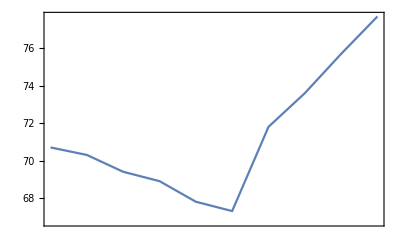

```mathematica
DateListPlot[Echo@Transpose[{times, MapAt[ToExpression,#,1]&/@temps}]]
```

```mathematica
DateListPlot[times, MapAt[ToExpression,#,1]&/@temps]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {DateObject[{2019,7,7,3,16,7.},Instant,Gregorian,-4.],DateObject[{2019,7,7,4,16,7.},Instant,Gregorian,-4.],«6»,DateObject[{2019,7,7,11,16,6.},Instant,Gregorian,-4.],DateObject[{2019,7,7,12,16,7.},Instant,Gregorian,-4.]} is not a valid dataset or list of datasets.

DateListPlot[{Sun 7 Jul 2019 03:16:07GMT-4.,Sun 7 Jul 2019 04:16:07GMT-4.,Sun 7 Jul 2019 05:16:07GMT-4.,Sun 7 Jul 2019 06:16:07GMT-4.,Sun 7 Jul 2019 07:16:06GMT-4.,Sun 7 Jul 2019 08:16:06GMT-4.,Sun 7 Jul 2019 09:16:07GMT-4.,Sun 7 Jul 2019 10:16:07GMT-4.,Sun 7 Jul 2019 11:16:06GMT-4.,Sun 7 Jul 2019 12:16:07GMT-4.},{70.7 °F,70.3 °F,69.4 °F,68.9 °F,67.8 °F,67.3 °F,71.8 °F,73.6 °F,75.7 °F,77.7 °F}]

```mathematica
data2[[1;;All,2,1,2,2]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,3]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,4]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,7]]
```

Dataset[<>]

```mathematica
data2[[1;;All,2,1,8]]
```

Dataset[<>]